```mathematica
卫星轨道频谱--快速算法
```

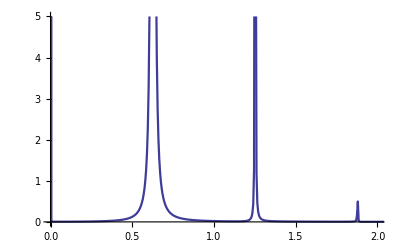

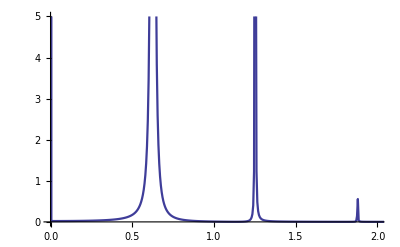

```mathematica
tm=200.0;coef=4 π^2;
xinitial={0,6.5};yinitial={1.1,0.8};
equ={x''[t]==-(coef*x[t])/((x[t]^2+y[t]^2)^(3/2)),
y''[t]==-(coef*y[t])/((x[t]^2+y[t]^2)^(3/2)),
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],
y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equ,{x,y},{t,0,tm},MaxSteps->∞];
{x,y}={x,y}/.s[[1]];
sample=5000;
signal=Table[x[t],{t,0,tm,tm/sample}];
ps=Abs[Fourier[signal]]^2;
len=Length[ps];
ps=Table[{(j-1)/tm,ps[[j]]},{j,len}];
ListLinePlot[ps,PlotRange->{{0,2},{0,5}},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Export["e:/data/orbit-x.dat",ps];
signal=Table[y[t],{t,0,tm,tm/sample}];
ps=Abs[Fourier[signal]]^2;
len=Length[ps];
ps=Table[{(j-1)/tm,ps[[j]]},{j,len}];
ListLinePlot[ps,PlotRange->{{0,2},{0,5}},
PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Export["e:/data/orbit-y.dat",ps];
Clear[x,y]
```